# DNA Denaturation Analysis

## Process Experimental Data

Follow along with your instructor as you work through the data analysis steps.

#### Import & Plot your experimental data - Exercise

In the evaluation cell below, the long string of text that looks like “.../Dropbox/asu/teaching....” is telling Mathematica where to find the file and must be replaced by YOU in order to point the correct file on YOUR computer. Note that we MUST assign the result to a variable, dnadata, in order to have access to the data later.
The simplest way to insert the correct file path is the following:
	1. Highlight the text corresponding to the old file path and delete it.
	2. click on “Insert” above 
	3. choose “File Path...” 
After you choose “File Path”, you should be provided with a file browser where you then locate your files in a more familiar fashion for your operating system. Replace the current string of characters in the Import command below, but DO NOT remove the “CSV” ending after the file path. Do you get the expected result?

```mathematica
dnadata=Import["~/Downloads/Processed DNA Data - van't Hoff.csv","CSV"]
```

{{1.15846×10^-6,0.00327869},{2.20219×10^-6,0.00328563},{3.33475×10^-6,0.00324568},{4.50432×10^-6,0.00323478},{5.55545×10^-6,0.00323211},{6.63249×10^-6,0.00323279}}

Now that you have your data ready, we can plot it. The shape will not be linear since the van’t Hoff equation contains a natural log of concentration

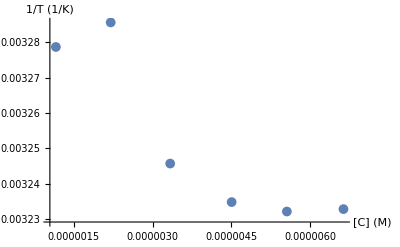

```mathematica
ListPlot[dnadata,PlotMarkers->{Automatic,Medium},AxesLabel->{Style["[C] (M)",14],Style["1/T (1/K)",14]},PlotRange->All]
```

#### Make expression for van’t Hoff equation - Example

The van’t Hoff equation can be represented using an expression in Mathematica as one of the steps involved in performing a nonlinear fit. Execute the cell below to store the van’t Hoff equation as equation7. 
The following symbols will be represented as words for simplicity: 
ΔH^0: DeltaH
ΔS^0 : DeltaS
Concentraiton : Conc 
Note that R = 8.314 J/(mol K) is used in order to set the units of the equation.

```mathematica
equation7=-R/DeltaH * Log[Conc]+(DeltaS+R Log[4])/DeltaH/.R->8.314 (*J/(mol K)*)
```

(11.5257+DeltaS)/DeltaH-(8.314 Log[Conc])/DeltaH

#### Perform the nonlinear fit and plot the result - Exercise

Now that the data and nonlinear model expression have been built, the NonlinearModelFit function can be used in order to perform the fit. 
Follow along with your instructor in order to complete this section. Make sure to name the output of this function nlmfit for ease of use later. The  proper output should be a “FittedModel.”

#### Extract the fit parameters & their uncertainties - Exercise

In your Mathematica homework assignment you were introduced to the “ParameterTable” option of a FittedModel. Use this approach to extract the numerical values for the enthalpy and entropy of dsDNA denaturation. 
What are the units of ΔH^0 and ΔS^0, and their uncertainties? Write each quantity succinctly as ΔH^0±δΔH^0 and ΔS^0±δSH^0.

#### Plot the fit and the experimental data together - Example

Execute the cell below in order to plot the fit and your experimental data together. This plot is saved to your computer and should be included in your writeups.

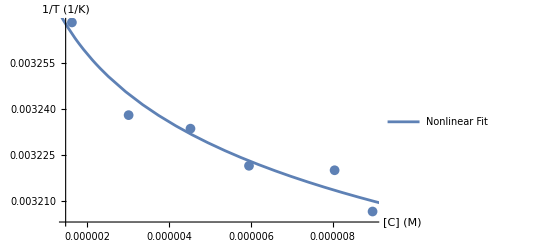

```mathematica
Plot[nlmfit[x],{x,1*10^-7,2*10^-5},PlotLegends->{"Nonlinear Fit"}];
ListPlot[dnadata,PlotMarkers->{Automatic,Medium},AxesLabel->{Style["[C] (M)",14],Style["1/T (1/K)",14]},PlotRange->All];
Show[%,%%]
Export["vantHoffPlot.png",%,"PNG"]
```

## Calculate Gibbs Free Energy and Eq. Constant

#### Calculate the Gibbs free energy @ 298.15 K - Exercise

With the enthalpy and entropy available from the previous section, calculate the Gibbs free energy @ 298.15 K. The equation is given in the lab manual, Eq. (5).
Is denaturation spontaneous at room temperature based on your result? Convert your result to kJ/mol when reporting for your writeups.

#### Calculate the equilibrium constant @ 298.15 K - Exercise

After calculating ΔG^0 in the previous Exercise, use the result to calculate the equilibrium constant. In order to do this, you must rearrange Eq. (5) as: 
K = Exp[ ... ]
where the ... are replaced by some symbols related to R, ΔG^0, and T. See Eq. (9) in the manual. 
Does the equilibrium of this process favor the reactants or products?

#### Calculate the uncertainty in Gibbs free energy @ 298.15 K - Exercise

After calculating the Gibbs free energy, you can calculate the relative error for this quantity based on Eq. (8) of the lab manual. Make sure the units are kJ/mol so that you can report the Gibbs free energy and uncertainty in your writeups as 
ΔG^0±δΔG^0.

#### Calculate the uncertainty in equilibrium constant @ 298.15 K - Exercise

After calculating the uncertainty in the Gibbs free energy, you can calculate the relative error for the eq. const based on Eq. (10) of the lab manual. You will need to represent K and δK using the same order of magnitude when reporting them in your writeup. For instance, K ± δK = (1.35 ± 0.53) x 10^-6 .